### Lotka-Volterra model for competing species.

```mathematica
(*manipulate with stab analysis*)
```

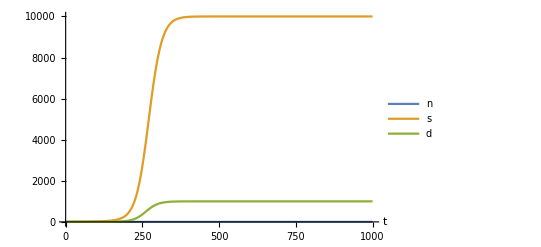

```mathematica
(*maybe restart Mathematica before*)
(*right hand sides of differential equations*)
Clear[pars, vars]
rhs[{n_,s_,d_}][{ϕ_, Ys_, Us_, hs_, ms_, δ_, xreq_, Kd_, r_}]:=
{
d*ϕ - (1/Ys)*((Us*n*s)/(1+Us*hs*n)),
(((Us*n*s)/(1+Us*hs*n)) - ms*s),
(r  (((s δ )/xreq)/(1+(s δ )/xreq)))*d*(1-d/Kd)
};
(*state variables*)
vars={n,s,d};
(*parameters*)
(*define standard set of parameters*)
pars={ϕ = 100, Ys = 0.01, Us = 10, hs = 1, ms = 0.1, δ = 2, xreq = 100, Kd = 1000, r = 0.05};
(*parameteres for simulation*)
n0=1;s0=1; d0=1;tmax=1000;
(*simulation*)
(*differential equations*)
eqs={{n'[t],s'[t], d'[t]}==rhs[{n[t],s[t], d[t]}][pars]};
(*initial conditions*)
inis=
{
n[0]==n0,
s[0]==s0,
d[0] == d0
};
(*state variables*)
vars={n,s,d};
(*solve the system of differential equations numerically*)
sol=NDSolve[
(*differential equations and initial conditions*)
Join[eqs,inis],
(*state variables*)
vars,
(*time span*)
{t,0,tmax}
];
(*plot simulation*)
Plot[
(*population densities*)
{
n[t]/.sol,
s[t]/.sol,
d[t]/.sol
},
(*time span*)
{t,0,tmax},
(*style*)
PlotLegends->{"n","s","d"},
AxesLabel->{"t"}
]
```

```mathematica
(*solve the equilibrium for a given set of parameters*)
solveeq[pars_,conditions_]:=NSolve[Join[{rhs[vars][pars]=={0,0,0}},conditions],{n,s,d}];
(*test it, there are multiple equilibria: both species present, only one species present, both species absent*)
solveeq[pars,{}]
```

{{n→0.0111111,d→1000.,s→10000.},{n→0.0111111-1.88031×10^-10 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},{n→0.0111111+2.01413×10^-10 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ}}

```mathematica
(*get only the positive equilibrium*)
solveeq[pars,{n>0,s>0, d >0}]
```

{{n→0.0111111,d→1000.,s→10000.}}

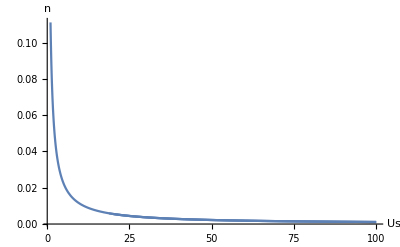

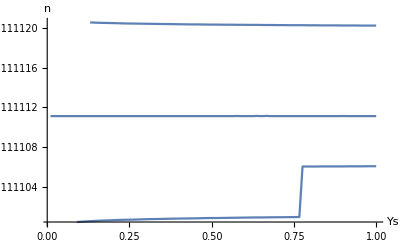

-Graphics-

```mathematica
(*now do the bifurcation, with say the parameter k1.*)
Plot[n/.solveeq[{ϕ, Ys, Usx, hs, ms, δ, xreq, Kd, r},{}],{Usx,1,100},PlotRange->Full,AxesLabel->{"Us","n"}]
Plot[n/.solveeq[{ϕ, Ysx, Us, hs, ms, δ, xreq, Kd, r},{}],{Ysx,0.01,1},PlotRange->Full,AxesLabel->{"Ys","n"}]
```

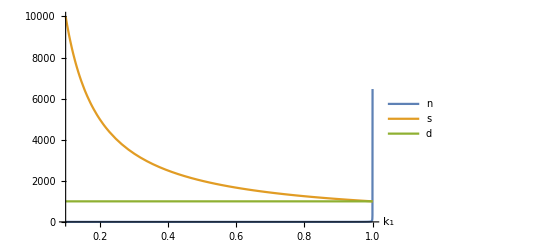

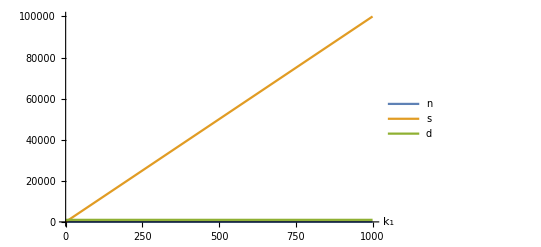

```mathematica
(*show both species. Only the equilibrium with both species present. When  k1 is big, the second species is getting outcompeted. I'm still trying to figure out how to call solveeq only once while still getting the colors right.*)
Plot[{
n/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}],
s/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}],
d/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}]
},
{msx,0.1,1},PlotRange->Full,AxesLabel->{"k_1"},PlotLegends->{"n","s", "d"}]

Plot[{
n/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}],
s/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}],
d/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}]
},
{ϕx,0, 1000},PlotRange->Full,AxesLabel->{"k_1"},PlotLegends->{"n","s", "d"}]
```

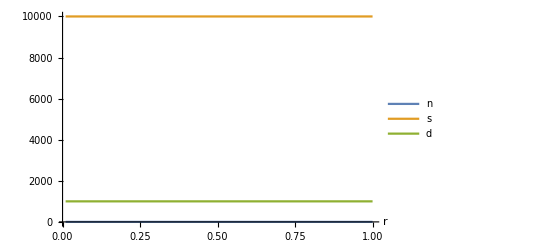

```mathematica
Plot[{
n/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}],
s/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}],
d/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}]
},
{rx,0.01, 1},PlotRange->Full,AxesLabel->{"r"},PlotLegends->{"n","s", "d"}]
```

```mathematica
(*stability? Eigenvalues of Jacobian Matrix*)
```

```mathematica
(*the jacobi matrix*)
jacobi[vars_,pars_]:=Table[D[rhs[vars][pars],var],{var,vars}];
(*example with example pars*)
(*from left to right:
equilibrium,
jacobi matrix,
eigenvalues,
max real part (all eigenvector in this example are real),
stability of equilibrium (unstable <-> Max@Re@Eigenvalue > 0)*)
Grid[
Table[
With[{j=jacobi[vars,pars]/.eq},
{
eq,
j//MatrixForm,
Eigenvalues@j,
Max@Re[Eigenvalues@j],
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,Evaluate@solveeq[pars,{}]}],
Frame->All]
```

{n→0.0111111,d→1000.,s→10000.} | (-8.1×10^6 | 81000. | 0
-10. | -2.77556×10^-17 | 2.74801×10^-21
100 | 0 | -0.0497512) | {-8.1×10^6,-0.1,-0.0497512} | -0.0497512 | Stable
{n→0.0111111-1.88031×10^-10 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ} | (0.00336089-0.00677196 ⅈ | -0.0000336089+0.0000677196 ⅈ | 0
-10.+1.52305×10^-7 ⅈ | -1.93936×10^-9-1.52305×10^-9 ⅈ | -4.14924×10^-10+8.36045×10^-10 ⅈ
100 | 0 | -4.14925×10^-9+8.36045×10^-9 ⅈ) | {0.0250248-0.0181342 ⅈ,-0.0216639+0.0113623 ⅈ,-8.29849×10^-9+1.67209×10^-8 ⅈ} | 0.0250248 | Unstable
{n→0.0111111+2.01413×10^-10 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ} | (-0.0036326+0.00721605 ⅈ | 0.000036326-0.0000721605 ⅈ | 0
-10.-1.63145×10^-7 ⅈ | 2.08237×10^-9+1.63145×10^-9 ⅈ | 4.4847×10^-10-8.9087×10^-10 ⅈ
100 | 0 | 4.4847×10^-9-8.90871×10^-9 ⅈ) | {0.0128073+0.0278326 ⅈ,-0.0164399-0.0206165 ⅈ,8.96939×10^-9-1.78174×10^-8 ⅈ} | 0.0128073 | Unstable

```mathematica
(*Make bifurcation of parameter k1 with stability analysis.*)
list=
Table[{msx,
With[{p={ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{msx,0,0.99,0.01}];
```

```mathematica
(*now we have a list of this structure*)
list[[1;;3]]
```

{{0.,{{{n→0,d→0,s→-28.3215-20.8607 ⅈ},Unstable}}},{0.01,{{{n→0.0010101,d→1000.,s→100000.},Stable},{{n→0.0010101,d→-5.9055×10^-8+1.2051×10^-7 ⅈ,s→-5.9055×10^-6+0.000012051 ⅈ},Unstable},{{n→0.0010101,d→6.01303×10^-8-1.17998×10^-7 ⅈ,s→6.01303×10^-6-0.0000117998 ⅈ},Unstable}}},{0.02,{{{n→0.00204082,d→1000.,s→50000.},Stable},{{n→0.00204082,d→-8.82873×10^-8+1.79272×10^-7 ⅈ,s→-4.41437×10^-6+8.96361×10^-6 ⅈ},Unstable},{{n→0.00204082,d→1.37301×10^-7-2.71696×10^-7 ⅈ,s→6.86504×10^-6-0.0000135848 ⅈ},Unstable}}}}

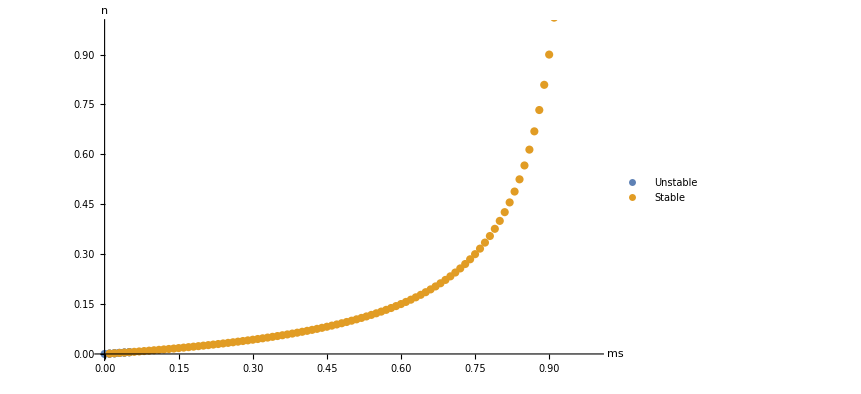
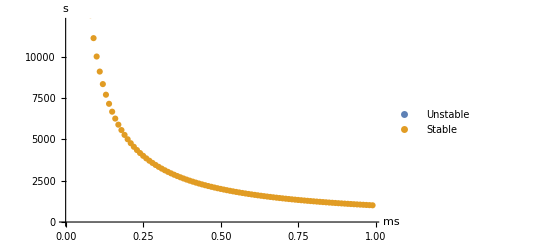
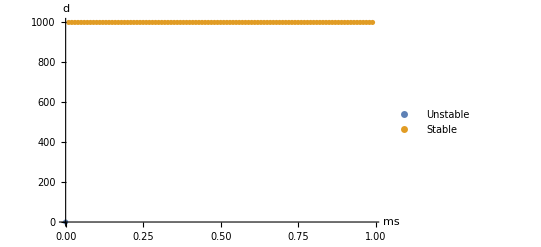

```mathematica
(*Plot: extract the Stable and Unstable equilibria of the different species from list*)
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"ms",var}],{
var,vars}]
```

```mathematica
(*The results are rather intuitive, as we increase the mortality of the Bee we increase the stable equilibrium of the pollen, decrease the stable equilibrium of the bees, and the stability of the plants stays the same *recall the analytical solution of our equations suggest that the plants will have a stable equilibrium at Kd*  *)
```

{{0.,{{{s→0.,d→0.},Stable}}},{0.5,{{{n→0.222222,d→1000.,s→10000.},Stable},{{n→0.222222-3.76063×10^-9 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},Unstable},{{n→0.222222+4.02826×10^-9 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ},Unstable}}},{1.,{{{n→0.111111,d→1000.,s→10000.},Stable},{{n→0.111111-1.88031×10^-9 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},Unstable},{{n→0.111111+2.01413×10^-9 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ},Unstable}}}}

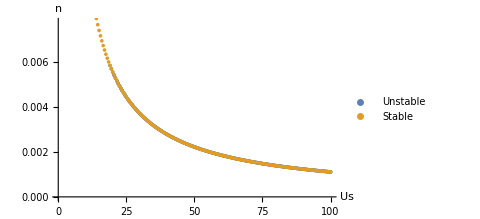
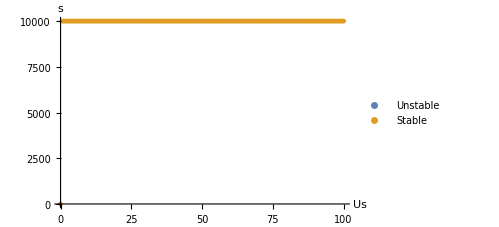
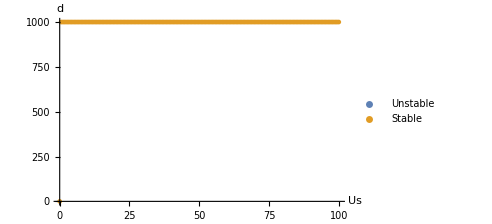

```mathematica
list=
Table[{Usx,
With[{p={ϕ, Ys, Usx, hs, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{Usx,0,100,0.5}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"Us",var}],{
var,vars}]
```

```mathematica
(*Its a bit interesting that Uptake only affects the equilibrium of Pollen and nothing else. As expected, if we increase the uptake rate of the pollen by bees we decrease the stable equilibrium of the pollen.*)
```

Power::infy: Infinite expression 1/0. encountered.

{{0.,{}},{0.01,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-1.88031×10^-10 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},Unstable},{{n→0.0111111+2.01413×10^-10 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ},Unstable}}},{0.02,{{{n→0.0111111,d→1000.,s→20000.},Stable},{{n→0.0111111-1.85553×10^-10 ⅈ,d→-2.59262×10^-7+5.23283×10^-7 ⅈ,s→-5.18525×10^-6+0.0000104657 ⅈ},Unstable},{{n→0.0111111+1.51712×10^-10 ⅈ,d→2.14197×10^-7-4.25643×10^-7 ⅈ,s→4.28394×10^-6-8.51287×10^-6 ⅈ},Unstable}}}}

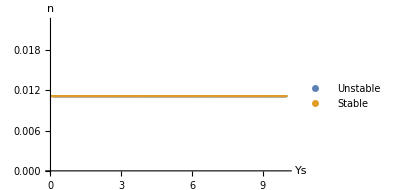
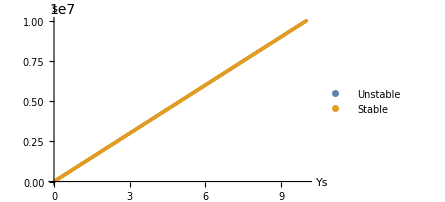
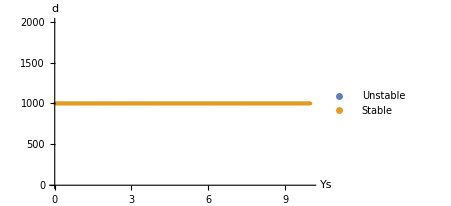

```mathematica
list=
Table[{Ysx,
With[{p={ϕ, Ysx, Us, hs, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{Ysx,0,10,0.01}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"Ys",var}],{
var,vars}]
```

```mathematica
(*Yield doesnt affect stable equilibria of the plants nor pollen, but linearly increases the stable equilibria of our bees*)
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(69046 d)/57903+(40299 n)/38602-(142003 s)/115806 == 1.

{{0.,{{{n→0.95789,s→0.,d→0.},Unstable},{{n→0.0111111,s→-0.73462,d→-0.073462},Unstable}}},{0.2,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-4.02397×10^-10 ⅈ,d→-4.04403×10^-6+8.12137×10^-6 ⅈ,s→-0.0000404403+0.0000812137 ⅈ},Unstable},{{n→0.0111111+7.73321×10^-10 ⅈ,d→7.79877×10^-6-0.0000155537 ⅈ,s→0.0000779877-0.000155537 ⅈ},Unstable}}},{0.4,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-4.12286×10^-10 ⅈ,d→-2.62545×10^-6+5.27752×10^-6 ⅈ,s→-0.0000262545+0.0000527752 ⅈ},Unstable},{{n→0.0111111+3.89853×10^-10 ⅈ,d→2.49435×10^-6-4.97049×10^-6 ⅈ,s→0.0000249435-0.0000497049 ⅈ},Unstable}}}}

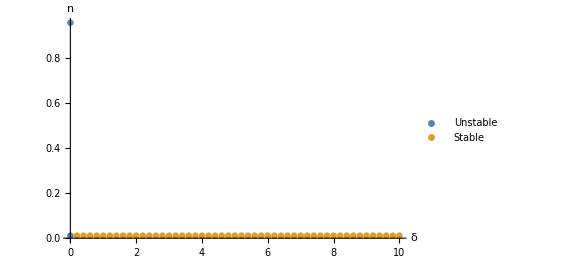
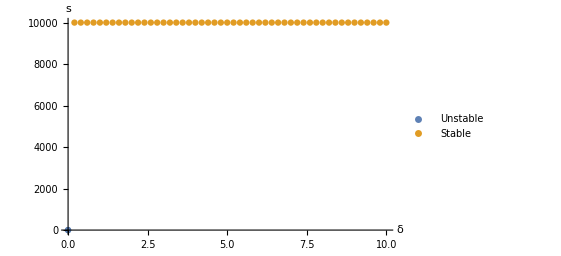
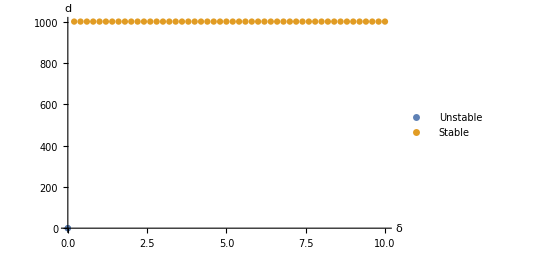

```mathematica
list=
Table[{δx,
With[{p={ϕ, Ys, Us, hs, ms, δx, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{δx,0,10,0.2}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"δ",var}],{
var,vars}]
```

```mathematica
(*Delta has no effect on the stable equilibria of our three state variables*)
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(69046 d)/57903+(40299 n)/38602-(142003 s)/115806 == 1.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{{0.,{{{n→0.95789,s→0.,d→0.},Unstable},{{n→0.0111111,s→-0.73462,d→-0.073462},Unstable}}},{0.01,{{{s→0.,d→0.},If[Max[0,90. Re[((-0.0111111+1. n) (0.1+1. n))/(1.+10. n)^2]]>0,Unstable,Stable]},{{n→0.0111111,s→0.,d→0.},Stable},{{n→0.0111111,s→10000.,d→1000.},If[Max[-1. Re[δx/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx-√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx+√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)]]>0,Unstable,Stable]}}},{0.02,{{{s→0.,d→0.},If[Max[0,90. Re[((-0.0111111+1. n) (0.1+1. n))/(1.+10. n)^2]]>0,Unstable,Stable]},{{n→0.0111111,s→0.,d→0.},Stable},{{n→0.0111111,s→10000.,d→1000.},If[Max[-2. Re[δx/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx-√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx+√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)]]>0,Unstable,Stable]}}}}

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::partd: Part specification m⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {m⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

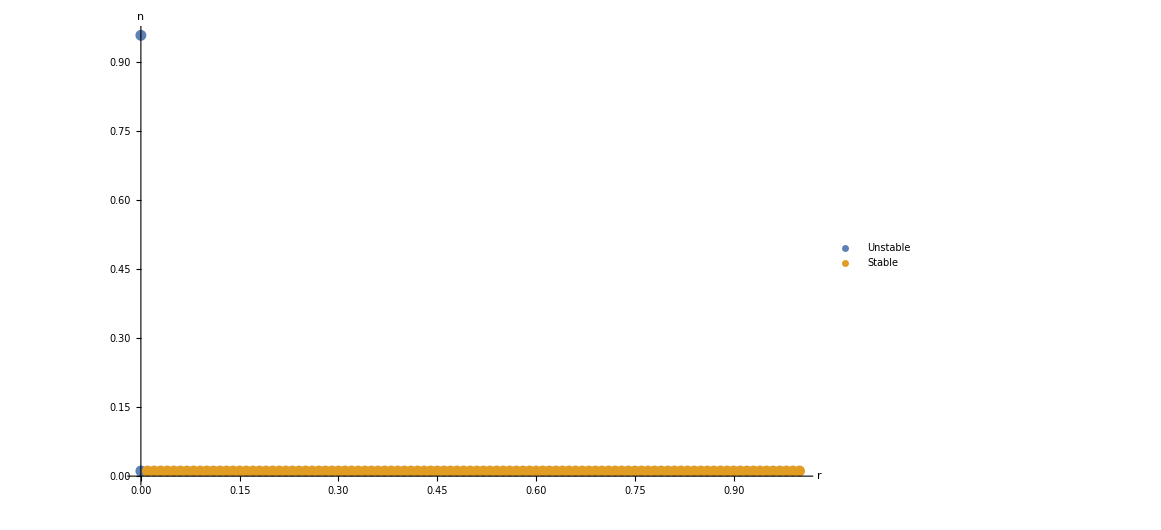
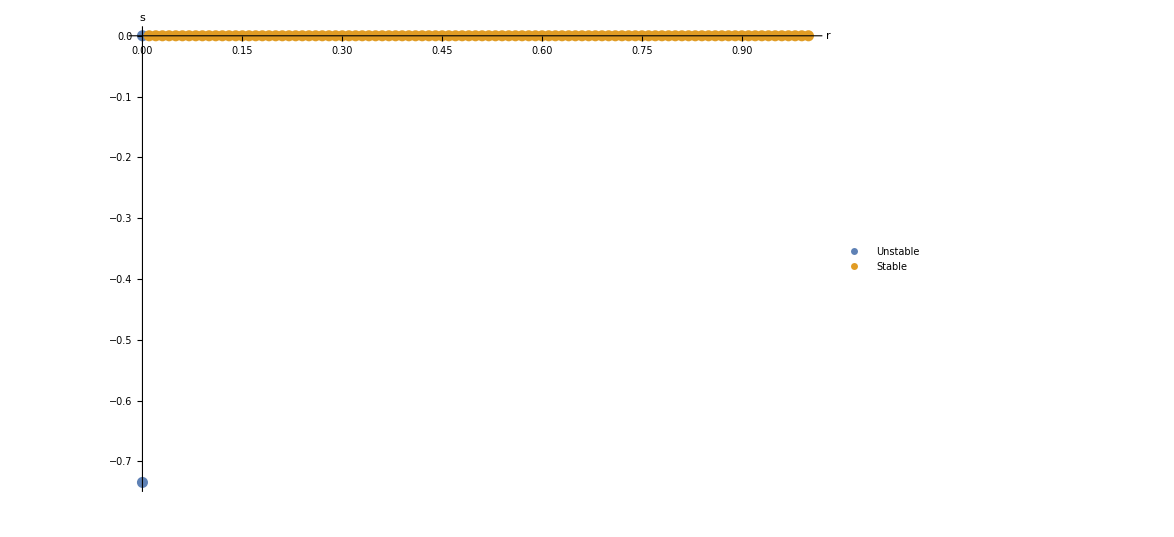
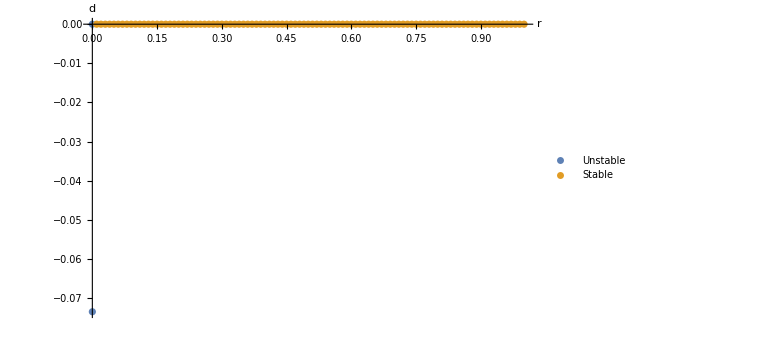

```mathematica
list=
Table[{rx,
With[{p={ϕ, Ys, Us, hs, ms, δx, xreq, Kd, rx}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{rx,0,1,0.01}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"r",var}],{
var,vars}]
```

```mathematica
(*Basically doesn't affect the system unless reproduction is waaaay to small. *)
```

{{1,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-4.24064×10^-9+8.72825×10^-9 ⅈ,s→-4.24064×10^-8+8.72825×10^-8 ⅈ},Unstable},{{n→0.0111111,d→7.74172×10^-9-1.51077×10^-8 ⅈ,s→7.74172×10^-8-1.51077×10^-7 ⅈ},Unstable}}},{2,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-1.36054×10^-8+2.78465×10^-8 ⅈ,s→-1.36054×10^-7+2.78465×10^-7 ⅈ},Unstable},{{n→0.0111111,d→1.23397×10^-8-2.42028×10^-8 ⅈ,s→1.23397×10^-7-2.42028×10^-7 ⅈ},Unstable}}},{3,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-1.79324×10^-8+3.66018×10^-8 ⅈ,s→-1.79324×10^-7+3.66018×10^-7 ⅈ},Unstable},{{n→0.0111111,d→1.62132×10^-8-3.18789×10^-8 ⅈ,s→1.62132×10^-7-3.18789×10^-7 ⅈ},Unstable}}}}

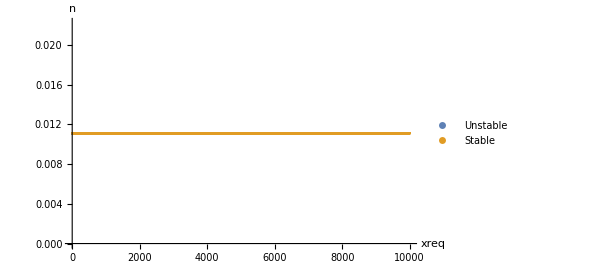
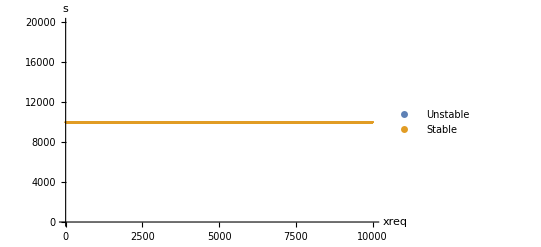
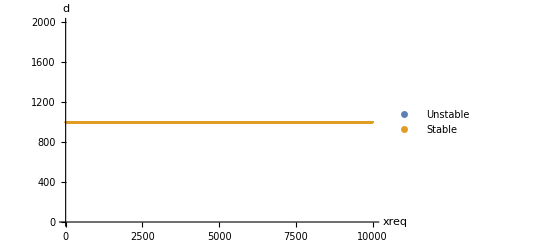

```mathematica
list=
Table[{xreqx,
With[{p={ϕ, Ys, Us, hs, ms, δ, xreqx, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{xreqx,1,10000,1}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"xreq",var}],{
var,vars}]
```

```mathematica
(*Does not affect the stable equilibria of the system*)
```

{{1,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-1.88031×10^-10 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},Unstable},{{n→0.0111111+2.01413×10^-10 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ},Unstable}}},{2,{{{n→0.0125,d→1000.,s→10000.},Stable},{{n→0.0125-4.73343×10^-10 ⅈ,d→-7.75195×10^-7+1.56136×10^-6 ⅈ,s→-7.75195×10^-6+0.0000156136 ⅈ},Unstable},{{n→0.0125+3.86879×10^-10 ⅈ,d→6.38992×10^-7-1.27195×10^-6 ⅈ,s→6.38992×10^-6-0.0000127195 ⅈ},Unstable}}},{3,{{{n→0.0142857,d→1000.,s→10000.},Stable},{{n→0.0142857-5.3317×10^-10 ⅈ,d→-6.44792×10^-7+1.29729×10^-6 ⅈ,s→-6.44792×10^-6+0.0000129729 ⅈ},Unstable},{{n→0.0142857+5.02794×10^-10 ⅈ,d→6.13243×10^-7-1.22096×10^-6 ⅈ,s→6.13243×10^-6-0.0000122096 ⅈ},Unstable}}}}

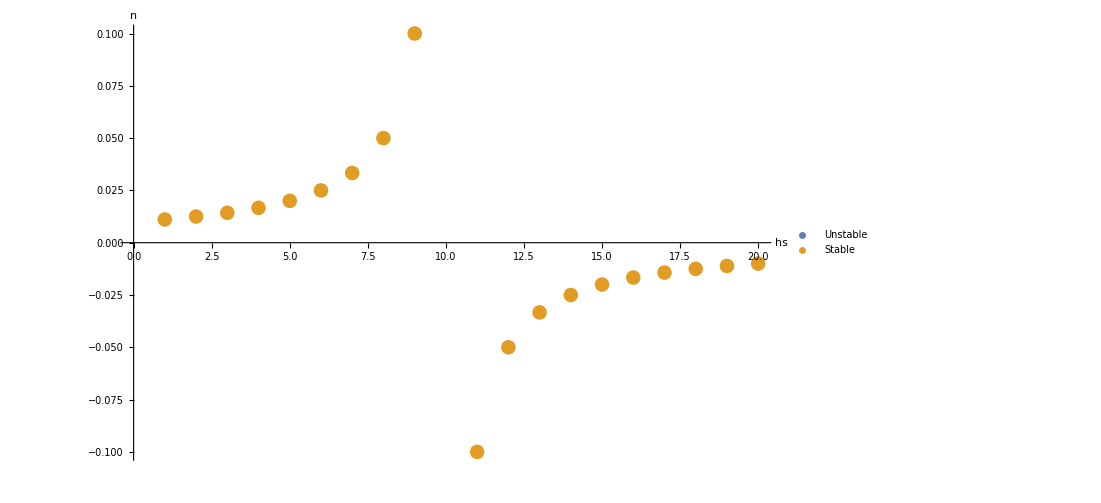
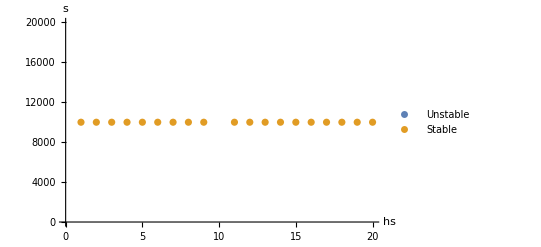
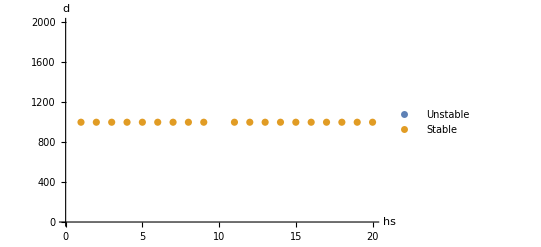

```mathematica
list=
Table[{hsx,
With[{p={ϕ, Ys, Us, hsx, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{hsx,1,20,1}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"hs",var}],{
var,vars}]
```

```mathematica
(*THere is a vertical asymptote at hs=10, once we surpass this we enter negative pollen land*)
```